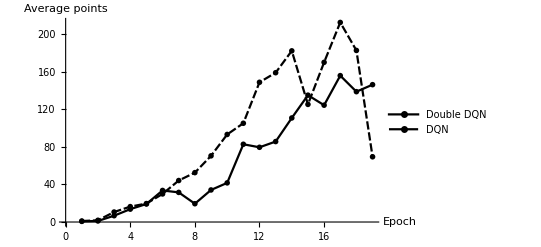

```mathematica
Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/double_dqn_results.csv"];
rewardper=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/double_dqn_results.csv"][[2;;,4]];
meanq=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/double_dqn_results.csv"][[2;;,5]];
naturerewardper=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/nature_results.csv"][[2;;-5,4]];
naturemeanq=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/nature_results.csv"][[2;;-5,5]];
rewardperplot=ListPlot[{rewardper,naturerewardper},PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Average points"},PlotLegends->{"Double DQN","DQN"}]
```

```mathematica
Export["/Users/cwalker32/Code/breakout_rl/presentation/dqn_rewardper.pdf",rewardperplot];
```

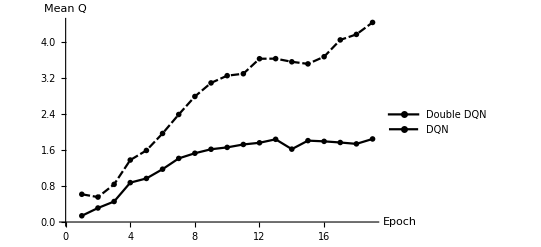

```mathematica
meanqplot=ListPlot[{meanq,naturemeanq},PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Mean Q"},PlotLegends->{"Double DQN","DQN"}]
```

```mathematica
Export["/Users/cwalker32/Code/breakout_rl/presentation/dqn_meanq.pdf",meanqplot];
```

```mathematica
meanq
```

{0.138173,0.310951,0.454679,0.873231,0.966261,1.17166,1.41066,1.52516,1.61355,1.65509,1.7197,1.75713,1.8342,1.61604,1.80471,1.78878,1.76338,1.73291,1.84204}

```mathematica
rewardper
```

{0.692913,1.12686,6.72619,13.7149,19.214,33.6548,31.5772,19.5027,34.1818,41.7231,82.9,79.6632,85.7717,110.935,135.242,124.551,156.071,138.952,146.432}

```mathematica
rewardper/meanq
```

{5.01483,3.6239,14.7933,15.706,19.8848,28.724,22.3847,12.7873,21.1843,25.2089,48.206,45.3372,46.7625,68.6459,74.9382,69.6289,88.5065,80.184,79.4943}

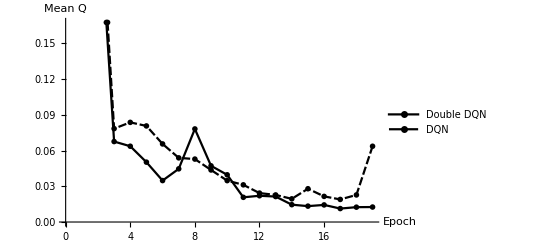

```mathematica
ListPlot[{meanq/rewardper,naturemeanq/naturerewardper},PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Mean Q"},PlotLegends->{"Double DQN","DQN"}]
```